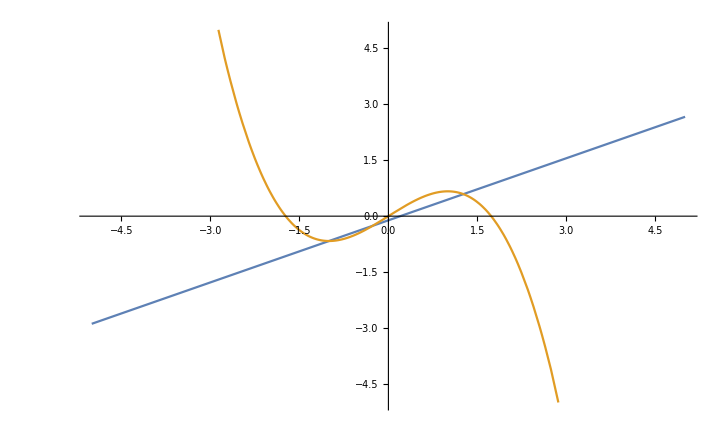

```mathematica
b = -0.2;
g = 1.8;
f[u_] := (u+b)/g;
h[u_] := u-(u^3)/3;
Plot[{f[u],h[u]},{u,-5,5},PlotRange->{-5,5}]
```

```mathematica
Solve[f[u] == h[u],u]
```

{{u→-1.},{u→-0.263763},{u→1.26376}}

```mathematica
f[-0.9999999999999999]
```

-0.666667

```mathematica
h[-0.9999999999999999]
```

-0.666667

```mathematica
f[1.2637626158259734]
```

0.590979

```mathematica
h[1.2637626158259734]
```

0.590979